# Lab 6 - Roots

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

Calculate the orbit for the pulsar

```mathematica
e=0.617139;
T=27906.98161;
c=299792458;
a=2.34186*c;
```

```mathematica
ts = Table[t, {t, -14000,28000,100}];
```

```mathematica
eqs = Map[Function[t,T/(2*Pi) * (x - e * Sin[x]) - t],ts];
```

```mathematica
zeros = Map[Function[f, FindRoot[f,{x, 0}]],eqs][[All,1,2]];
```

```mathematica
rs = Map[Function[z, a*(1-e*Cos[z])], zeros];
```

```mathematica
xs =  Map[Function[z, a*(Cos[z]-e)], zeros];
```

```mathematica
ys =  Map[Function[z, a*(Sqrt[1-e^2]*Sin[z])], zeros];
```

```mathematica
data = Transpose[{xs, ys}];
```

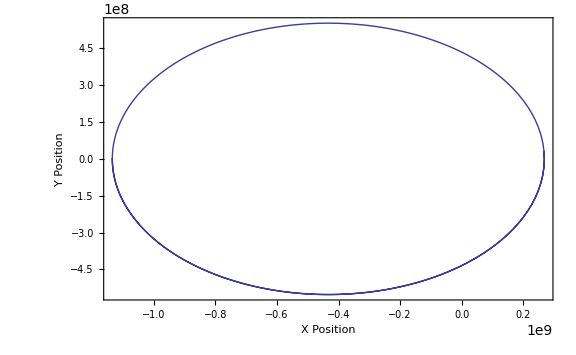

```mathematica
graph = ListPlot[data, Joined -> True, AxesOrigin -> {-4*10^8,0}, Frame -> True, FrameLabel->{{"Y Position", ""},{"X Position", "Orbit of Binary Pulsar 1913+16"}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["orbitMath.png", graph]
```

orbitMath.png

```mathematica
Export["orbitCalc.pdf", EvaluationNotebook[]]
```

orbitCalc.pdf